```mathematica
Clear[Lx,Ly,m0,filename,ChernMatrixSiteWiseList,BinCountTable]
```

```mathematica
(**----------Data analysis of Local Chern Number-----------**)
```

```mathematica
Lx = 20;
Ly = 20;
m0 = -2.5;
```

```mathematica
location="data/";
```

```mathematica
filenameString1 = "datalocalChernLx=";
filenameString2="Ly=";
filenameString3 = "m0=";
```

```mathematica
filename = StringJoin[location,filenameString1,ToString[Lx],filenameString2,ToString[Ly],filenameString3,ToString[m0],".dat"]
```

data/datalocalChernLx=20Ly=20m0=-2.5.dat

```mathematica
ChernMatrixSiteWiseList=Flatten[Import[filename]];
```

```mathematica
ApproxChern = Round[Commonest[Round[ChernMatrixSiteWiseList,0.01]]][[1]]
```

0

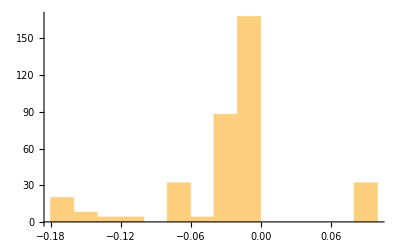

```mathematica
Histogram[ChernMatrixSiteWiseList]
```

```mathematica
BinCountTable = Table[BinCounts[ChernMatrixSiteWiseList,{ApproxChern-delta,ApproxChern+delta,2delta}][[1]],{delta,{0.1,0.3,0.5,0.7,0.9}}]
```

{324,376,396,396,400}

```mathematica
percentageOfSitesInsideBin=N[BinCountTable/(Lx*Ly)]
```

{0.81,0.94,0.99,0.99,1.}